## Introduced Top Predator (P): naivete toward P

Define Model

```mathematica
(* Modeling naïveté -- Introduce rho ρ which modifies the level of recognition of the predator by the basal resource by modifying the fitness equations. Now instead of the prey optimizing true per capita growth rate (true fitness) it will alter its level of effort to maximize "perceived fitness" based on a ρ-modified perception of the trophic-landscape.  Percived fitness alters the replicator equations (effort) which in turn affect the growth rates of the species. Effort shows up in the d equations so this modifies the effect of defense. Does not result in costly trait-modification because it does not show up in the cost equations no NCEs *)
```

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(* percieved fitness is defined as the per capita growth rate of the resource, but modified by a ρ parameter that varies from 1 (full recgnition) to zero (complete naïveté)*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) - (1-ρ) aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.2, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ρ->1};
parsCoex = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
```

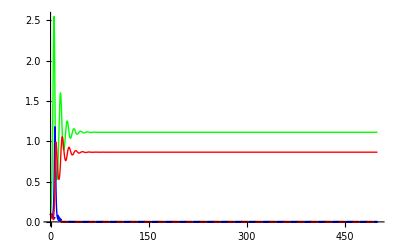

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsCoex},{R,Ν, P, eΝ, eP},{t,0,500}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,500}, PlotStyle-> cols]
```

### Manipulate across gradients of ρ

```mathematica
parsρ = {r-> 1,k-> 5, c0->0.15, fΝ->0.8,  fP->0.8,aPR-> 0.5, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1};
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsρ,{ρ->Ρ}]},
{R,Ν, P, eΝ, eP},{t,0,10000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Ρ,0.5,"ρ"},0,1}]
```

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {{R'[t]==R[t] (r Plus[«2»]-aPR Plus[«2»] P[«1»]-Power[«2»] R[«1»]-aΝR Plus[«2»] Ν[«1»]),R[0]==0.1},{Ν'[t]==(-mΝ-aPΝ P[«1»]+aΝR bΝR Plus[«2»] R[«1»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (-mP+aPR bPR Plus[«2»] R[«1»]+aPΝ bPΝ Ν[«1»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (c0 r Plus[«3»]-aPR fP eP[«1»] P[«1»]-aΝR fΝ Plus[«2»] Ν[«1»]),eΝ[0]==0.1},{eP'[t]==-v eP[t] (-c0 r Plus[«3»]+aPR fP Plus[«2»] P[«1»]+aΝR fΝ eΝ[«1»] Ν[«1»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}] in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==-v eP[t] (Times[«4»]+Times[«4»]+Times[«4»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==-v eP[t] (Times[«4»]+Times[«4»]+Times[«4»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of … in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
kparsρH = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
kparsρM = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
kparsρL = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8, aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρM },{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρL},{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝH = Plot[Evaluate[eΝ[k][500]/.kfinalH,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePH = Plot[Evaluate[eP[k][500]/.kfinalH,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝM = Plot[Evaluate[eΝ[k][500]/.kfinalM,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePM = Plot[Evaluate[eP[k][500]/.kfinalM,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝL = Plot[Evaluate[eΝ[k][500]/.kfinalL,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePL= Plot[Evaluate[eP[k][500]/.kfinalL,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

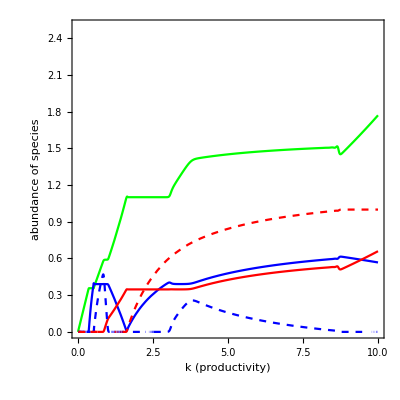

```mathematica
Show[kfinalRH,kfinalΝH,kfinalPH,kfinaleΝH, kfinalePH, Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

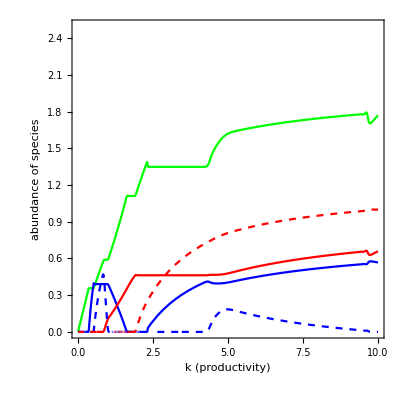

```mathematica
Show[kfinalRM,kfinalΝM, kfinalPM,kfinaleΝM, kfinalePM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

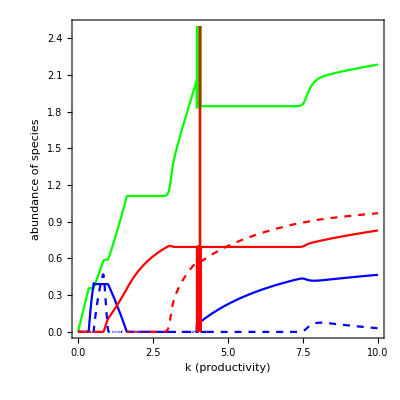

```mathematica
Show[kfinalRL,kfinalΝL,kfinalPL,kfinaleΝL, kfinalePL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

### Final Densities across cost

```mathematica
c0parsρH = {r-> 1, k->5, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
c0parsρM = {r-> 1, k->5, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
c0parsρL = {r-> 1, k->5, fΝ->0.8,fP->0.8, aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρH},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρM },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρL},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePL= Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

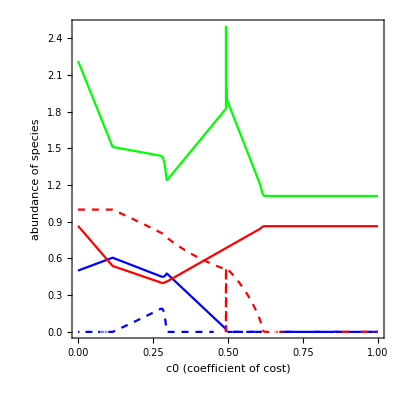

```mathematica
Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

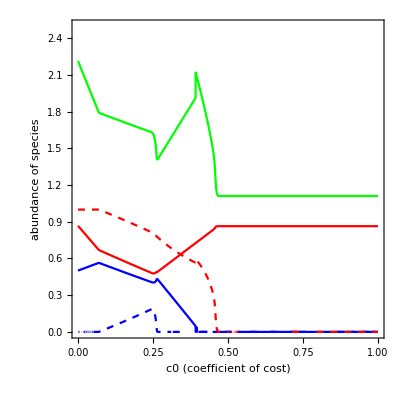

```mathematica
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePM, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

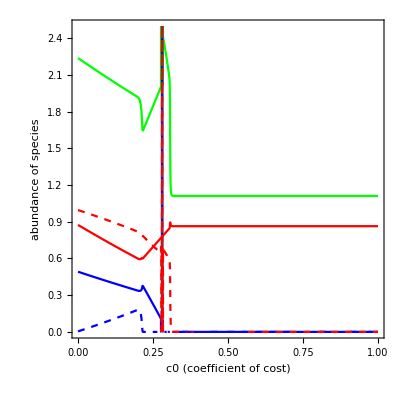

```mathematica
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

### Final densities of RNP across relative efficiencies of toward P (ρ)

```mathematica
parsStabρ = {r-> 0.9,k-> 5, c0->0.1, fΝ->0.7,  fP->0.7,aPR-> 0.5, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.6, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.25, v-> 1};
```

```mathematica
finalρ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsStabρ},{R,Ν, P, eΝ, eP},{t,0,10000}, {ρ}];
finalρR = Plot[Evaluate[R[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Green} ,
PlotRange->{{0,1},{0,3}}];
finalρΝ = Plot[Evaluate[Ν[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Blue},
PlotRange->{{0,1},{0,3}}];
finalρP = Plot[Evaluate[P[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Red},
PlotRange->{{0,1},{0,3}}];
finalρeΝ = Plot[Evaluate[eΝ[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle->{Thickness[0.015],Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
finalρeP = Plot[Evaluate[eP[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015],Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

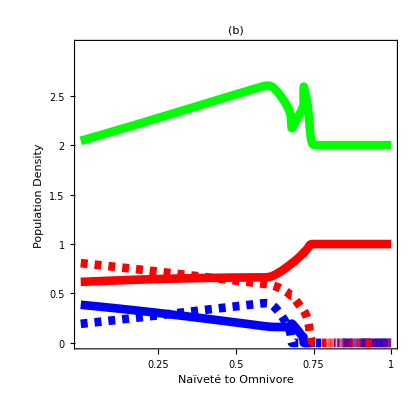

```mathematica
Fig4b =Show[finalρR,finalρΝ,finalρeΝ, finalρP, finalρeP,Frame-> True, FrameLabel->{"Naïveté to Omnivore","Population Density", "","Defense Effort"}, 
PlotLabel -> Style["(b)                                                                                       ", FontSize->14,  Bold],
ImageSize -> 414,Spacings-> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, FontSize-> 11};
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.5,1, 1.5, 2, 2.5},{0,0.5,1, 1.5, 2, 2.5}},{{1, 0.75, 0.5,0.25}, {None}}}]
```

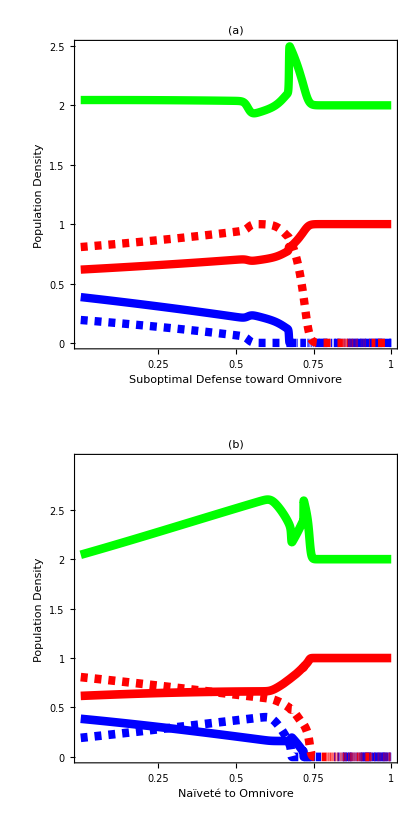
-Graphics-Novelty Gradient

```mathematica
Fig2ab =  Panel[GraphicsColumn[{Fig4a,Fig4b}, ImageSize-> 216, Spacings->{0,0}], 
{"Novelty Gradient",Rotate["Population Density / Defense Effort",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Larger];
Fig4ab =  Panel[GraphicsColumn[{Fig4a,Fig4b}, ImageSize-> 414, Spacings->0], 
{"Novelty Gradient",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Large]
```

```mathematica
Export["C:\\Users\\ingemank\\Desktop\\MoNSTR\\Dissertation Figures\\MoNSTR_Fig4_Full.tif",Fig4ab,"TIFF", ImageResolution-> 600]
```

C:\Users\ingemank\Desktop\MoNSTR\Dissertation Figures\MoNSTR_Fig4_Full.tif

Solve for equilibria

### Equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1-eP | 
R→0 | Ν→0 | P→0 | eΝ→1-eP | 
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→(k (aΝR (fΝ-1) mP+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | P→(aΝR (fΝ-1) k (-aΝR bΝR (fΝ-1) mP+aPΝ bΝR bPΝ (c0-1) r-aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aΝR aPR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aΝR aPR bPR k r (fΝ-c0))/(aΝR aPR^2 bPR fΝ k) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ r (aPΝ bPΝ c0+aΝR aPR k (bΝR bPΝ c0+bPR (fΝ-c0))))/(aΝR aPR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→0
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→-(-(√k √r √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √ρ)+c0 k r-fP k r)/(2 fP) | Ν→0 | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→-((√ρ √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √k √r)-c0 (ρ-2)-fP ρ)/(2 c0 fP (ρ-1))
R→-((√k √r √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √ρ)+c0 k r-fP k r)/(2 fP) | Ν→0 | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→((√ρ √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √k √r)+c0 (ρ-2)+fP ρ)/(2 c0 fP (ρ-1))
R→(-aΝR aPR^2 bPR fP k mΝ ρ ((fΝ-1) fP-fΝ) (bΝR bPΝ (ρ-2)+bPR)+(bΝR bPΝ ρ-bPR) √(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ (fP-1)-fP) (bΝR bPΝ ρ-2 bPR ρ+bPR)-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→-(ρ (aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ))))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→(bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ))+aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ))/(2 aPΝ aPR fP (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP-1) (ρ-2)+fP ρ)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ-fP (fΝ-2 ρ+1))-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP ρ+ρ-2)-fP ρ)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP ((fΝ-1) fP (2 ρ-1)-fΝ)+aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(-aΝR aPR^2 bPR fP k mΝ ρ ((fΝ-1) fP-fΝ) (bΝR bPΝ (ρ-2)+bPR)+(bPR-bΝR bPΝ ρ) √(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ (fP-1)-fP) (bΝR bPΝ ρ-2 bPR ρ+bPR)-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→-(ρ (bΝR bPR ((fΝ-1) fP-fΝ) (aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))))))+aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→(aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))))/(2 aPΝ aPR fP (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP-1) (ρ-2)+fP ρ)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ-fP (fΝ-2 ρ+1))-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP ρ+ρ-2)-fP ρ)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP ((fΝ-1) fP (2 ρ-1)-fΝ)+aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP)))-aΝR aPR bPR fP k ρ r (c0 (fΝ+fP)-fΝ fP))/(2 aΝR aPR bPR fΝ fP^2 ρ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fP ρ) | eΝ→-(aΝR aPR^2 bPR fP^2 k mΝ ρ^2 r (c0 (fΝ+fP)-fΝ fP)+aPR fP ρ (aΝR c0 k r (aPΝ r (2 bΝR bPΝ c0 fP (ρ-1)+bPR (c0 (fΝ+fP)-fΝ fP))-2 aΝR bΝR fΝ fP mP (ρ-1))+mΝ √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))+aPΝ c0 r √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bΝR c0 fΝ fP^2 k (ρ-1) ρ r (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→(aΝR aPR bPR fP k r (c0 (fΝ (ρ-2)-fP ρ)+fΝ fP ρ)-√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR c0 fΝ fP^2 k (ρ-1) r)
R→-(aΝR aPR bPR fP k ρ r (c0 (fΝ+fP)-fΝ fP)+√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR fΝ fP^2 ρ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fP ρ) | eΝ→(aΝR (-aPR^2) bPR fP^2 k mΝ ρ^2 r (c0 (fΝ+fP)-fΝ fP)+aPR fP ρ (aΝR c0 k r (2 aΝR bΝR fΝ fP mP (ρ-1)-aPΝ r (2 bΝR bPΝ c0 fP (ρ-1)+bPR (c0 (fΝ+fP)-fΝ fP)))+mΝ √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))+aPΝ c0 r √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bΝR c0 fΝ fP^2 k (ρ-1) ρ r (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→(aΝR aPR bPR fP k r (c0 (fΝ (ρ-2)-fP ρ)+fΝ fP ρ)+√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR c0 fΝ fP^2 k (ρ-1) r)
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→(aPΝ c0 r+aPR fP mΝ ρ)/(aΝR aPR bΝR fP ρ) | Ν→(-aPΝ^2 bPR c0^2 r^2+aPR fP ρ (aΝR bΝR k r (aΝR bΝR c0 mP (ρ-1)+aPR bPR mΝ ρ (fP-c0))-aPR bPR fP mΝ^2 ρ)+aPΝ aPR bPR c0 ρ r (aΝR bΝR k r (fP-c0)-2 fP mΝ))/(aΝR^2 aPR bΝR fP k ρ (aPΝ c0 r (bΝR bPΝ (ρ-1)+bPR)+aPR bPR fP mΝ ρ)) | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→(aPR fP ρ (aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)-aPΝ c0 r (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)))/(aΝR aPR fP k (aPΝ c0 r (bΝR bPΝ (ρ-1)+bPR)+aPR bPR fP mΝ ρ))
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(aΝR bΝR (c0-1) (fΝ-1) k r-mΝ)/(aΝR^2 bΝR (fΝ-1)^2 k) | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)-1/fΝ+1
R→(k r (fΝ-c0))/fΝ | Ν→(c0 r)/(aΝR fΝ) | P→0 | eΝ→mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r)+1/fΝ | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm;
JRΝ//MatrixForm;
JRP//MatrixForm;
```

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
parsCoexH = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.99};
parsCoexM = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
parsCoexL = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
subpars=Delete[parsCoexH,2];
subparsM=Delete[parsCoexM,2];
subparsL=Delete[parsCoexL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq20RΝ=JRΝ/.equil[[20,All]]//FullSimplify;
Jeq24RΝ=JRΝ/.equil[[24,All]]//FullSimplify;
Jeq22RΝ=JRΝ/.equil[[22,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq12RP=JRP/.equil[[12,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
```

```mathematica
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.subpars],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.subpars],#≥0&];
AllFeas12[k_]=AllTrue[Re[equil[[12,All,2]]/.subpars],#≥0&];
AllFeas20[k_]=AllTrue[Re[equil[[20,All,2]]/.subpars],#≥0&];
AllFeas22[k_]=AllTrue[Re[equil[[22,All,2]]/.subpars],#≥0&];
AllFeas24[k_]=AllTrue[Re[equil[[24,All,2]]/.subpars],#≥0&];

AllFeas6M[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas10M[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas12M[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsM],#≥0&];
AllFeas20M[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsM],#≥0&];
AllFeas22M[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsM],#≥0&];
AllFeas24M[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsM],#≥0&];

AllFeas6L[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas10L[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas12L[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsL],#≥0&];
AllFeas20L[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsL],#≥0&];
AllFeas22L[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsL],#≥0&];
AllFeas24L[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig20RΝ[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subpars]]]]; 
pReEig24RΝ[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subpars]]]];
pReEig22RΝ[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subpars]]]];

pReEig20RΝM[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsM]]]]; 
pReEig24RΝM[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsM]]]];
pReEig22RΝM[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsM]]]];

pReEig20RΝL[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsL]]]]; 
pReEig24RΝL[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsL]]]];
pReEig22RΝL[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsL]]]];
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subpars]]]];
pReEig12RP[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subpars]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subpars]]]];

pReEig6RPM[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig12RPM[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsM]]]];
pReEig10RPM[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];

pReEig6RPL[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig12RPL[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsL]]]];
pReEig10RPL[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
```

Produce plots

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsCoexH, {{2},{7}}];
kaPΝparsM = Delete[parsCoexM, {{2},{7}}];
kaPΝparsL = Delete[parsCoexL, {{2},{7}}];
```

#### new

```mathematica
RstarRN20 = equil[[20,1,2]];
NstarRN20= equil[[20,2,2]];
RstarRN24 = equil[[24,1,2]];
NstarRN24= equil[[24,2,2]];
RstarRN22 = equil[[22,1,2]];
NstarRN22= equil[[22,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN20 = bPR aPR (1 -0*fP)RstarRN20  + aPΝ bPΝ NstarRN20 - mP;
PinvRN24 = bPR aPR (1 -0*fP)RstarRN24  + aPΝ bPΝ NstarRN24 - mP;
PinvRN22 = bPR aPR (1 -0*fP)RstarRN22  + aPΝ bPΝ NstarRN22 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.kaPΝparsH;
PlotRN20 = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝ[x]<0&&AllFeas20[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.kaPΝparsH;
PlotRN24 = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝ[x]<0&&AllFeas24[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.kaPΝparsH;
PlotRN22 = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝ[x]<0&&AllFeas22[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝparsH;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.12,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.kaPΝparsH;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Fig2aa = Show[PlotRN20, PlotRN24,PlotRN22,PlotRP6,PlotRP12, PlotRP10, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.5,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.22,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.35,0.05}]]}],
Graphics[{Blue,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.22,0.05}],Scaled[{0.05,0.02}]}]}],
Graphics[{Red,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.8,0.9}],Scaled[{0.96,0.9}]}]}],PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],Frame->True, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},FrameTicks->{{{2,3, 4},{None}},{{None}, {None}}}]
```

-Graphics-

#### Medium naivete (ρ = 0.75)

```mathematica
PinvRN20kaPN = plotPinvRN20/.kaPΝparsM;
PlotRN20 = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

PinvRN24kaPN = plotPinvRN24/.kaPΝparsM;
PlotRN24 = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

PinvRN22kaPN = plotPinvRN22/.kaPΝparsM;
PlotRN22 = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝM[x]<0&&AllFeas22M[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsM;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.12,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

Νinv12kaPN = plotΝinv12/.kaPΝparsM;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RPM[x]<0&&AllFeas12M[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsM;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];
```

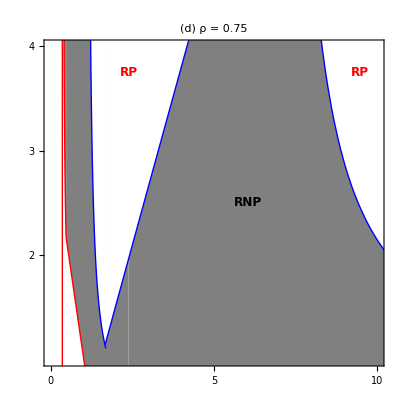

```mathematica
Fig2d=Show[PlotRN20, PlotRN24,PlotRN22,PlotRP6,PlotRP12, PlotRP10,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.6,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.93,0.9}]]}],
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},FrameTicks->{{{2,3, 4},{None}},{{0, 5, 10}, {None}}}]
```

#### Low relative efficiency (ρ = 0.5)

```mathematica
PinvRN20kaPN = plotPinvRN20/.kaPΝparsL;
PlotRN20L = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

PinvRN24kaPN = plotPinvRN24/.kaPΝparsL;
PlotRN24L = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

PinvRN22kaPN = plotPinvRN22/.kaPΝparsL;
PlotRN22L = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝL[x]<0&&AllFeas22L[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsL;
PlotRP6L = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

Νinv12kaPN = plotΝinv12/.kaPΝparsL;
PlotRP12L = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RPL[x]<0&&AllFeas12L[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsL;
PlotRP10L = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];
```

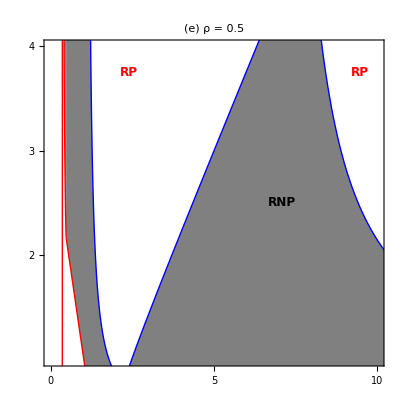

```mathematica
Fig2e =Show[PlotRN20L, PlotRN24L,PlotRN22L,PlotRP6L,PlotRP12L, PlotRP10L,Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.93,0.9}]]}],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},
PlotLabel -> Style["(e)    ρ = 0.5", FontSize->14,  Bold], 
FrameTicks->{{{2,3, 4},{None}},{{0, 5, 10}, {None}}}]
```

```mathematica
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.1}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.225}]}]}],
```

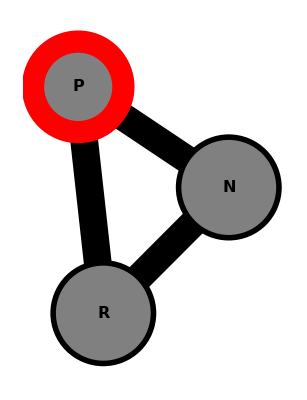

```mathematica
igpO=
Show[
Graphics[{{GrayLevel[0],Thickness[0.05],
Line[{{0.1, 0.1},{.6,.6}}], 
Line[{{0.6, 0.6},{0,1}}], 
Line[{{0.1, 0.1},{0,1}}] 
}}],
Graphics[{{GrayLevel[0.5],Disk[{.1,.1},.2]},{GrayLevel[0.5], Disk[{.6,.6},.2]}, {GrayLevel[0.5],Disk[{0,1.0},.2]}, {Red,Thickness[0.04],Circle[{0,1.0},.18]}, 
{Black,Thickness[0.01],Circle[{0.1,0.1},.2]}, 
{Black,Thickness[0.01],Circle[{0.6,0.6},.2]}}],
Graphics[{Text[Style["R",16,Black , Bold],{0.1,0.1}], 
Text[Style["N",16,Black , Bold],{0.6,0.6}],
Text[Style["P",16,Black , Bold],{0,1}]}]]
```

```mathematica
Figure2abcde = Panel[GraphicsGrid[{{Fig2aa,Fig2b, Fig2c},{igpO, Fig2d, Fig2e}}, ImageSize-> 518, Spacings->{0,20}], {"Productivity",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

-Graphics-ProductivityIGP strength

```mathematica
Figure2abcdeDIS = Panel[GraphicsGrid[{{Fig2aa,Fig2b, Fig2c},{igpO, Fig2d, Fig2e}}, ImageSize-> 414, Spacings->{0,20}], {"Productivity",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

-Graphics-ProductivityIGP strength

```mathematica
Export["C:\\Users\\ingemank\\Desktop\\MoNSTR\\Dissertation Figures\\MoNSTR_Fig2_Full.tif",Figure2abcdeDIS,"TIFF", ImageResolution->600]
```

C:\Users\ingemank\Desktop\MoNSTR\Dissertation Figures\MoNSTR_Fig2_Full.tif

```mathematica
Export["MoNSTR_Fig2_Full.pdf",Figure2abcde]
```

MoNSTR_Fig2_Full.pdf

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
parsCoexH = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.99};
parsCoexM = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
parsCoexL = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
subpars=Delete[parsCoexH,3];
subparsM=Delete[parsCoexM,3];
subparsL=Delete[parsCoexL,3];
```

```mathematica
AllFeas6[c0_]=AllTrue[Re[equil[[6,All,2]]/.subpars],#≥0&];
AllFeas10[c0_]=AllTrue[Re[equil[[10,All,2]]/.subpars],#≥0&];
AllFeas12[c0_]=AllTrue[Re[equil[[12,All,2]]/.subpars],#≥0&];
AllFeas20[c0_]=AllTrue[Re[equil[[20,All,2]]/.subpars],#≥0&];
AllFeas22[c0_]=AllTrue[Re[equil[[22,All,2]]/.subpars],#≥0&];
AllFeas24[c0_]=AllTrue[Re[equil[[24,All,2]]/.subpars],#≥0&];

AllFeas6M[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas10M[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas12M[c0_]=AllTrue[Re[equil[[12,All,2]]/.subparsM],#≥0&];
AllFeas20M[c0_]=AllTrue[Re[equil[[20,All,2]]/.subparsM],#≥0&];
AllFeas22M[c0_]=AllTrue[Re[equil[[22,All,2]]/.subparsM],#≥0&];
AllFeas24M[c0_]=AllTrue[Re[equil[[24,All,2]]/.subparsM],#≥0&];

AllFeas6L[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas10L[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas12L[c0_]=AllTrue[Re[equil[[12,All,2]]/.subparsL],#≥0&];
AllFeas20L[c0_]=AllTrue[Re[equil[[20,All,2]]/.subparsL],#≥0&];
AllFeas22L[c0_]=AllTrue[Re[equil[[22,All,2]]/.subparsL],#≥0&];
AllFeas24L[c0_]=AllTrue[Re[equil[[24,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig20RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subpars]]]]; 
pReEig24RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subpars]]]];
pReEig22RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subpars]]]];

pReEig20RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsM]]]]; 
pReEig24RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsM]]]];
pReEig22RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsM]]]];

pReEig20RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsL]]]]; 
pReEig24RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsL]]]];
pReEig22RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsL]]]];
```

```mathematica
pReEig6RP[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subpars]]]];
pReEig12RP[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subpars]]]];
pReEig10RP[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subpars]]]];

pReEig6RPM[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig12RPM[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsM]]]];
pReEig10RPM[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];

pReEig6RPL[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig12RPL[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsL]]]];
pReEig10RPL[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH = Delete[parsCoexH, {{3},{7}}];
c0aPΝparsM = Delete[parsCoexM, {{3},{7}}];
c0aPΝparsL = Delete[parsCoexL, {{3},{7}}];
```

### Invasibility Plot (k and aPN)

```mathematica
RstarRN20 = equil[[20,1,2]];
NstarRN20= equil[[20,2,2]];
RstarRN24 = equil[[24,1,2]];
NstarRN24= equil[[24,2,2]];
RstarRN22 = equil[[22,1,2]];
NstarRN22= equil[[22,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN20 = bPR aPR (1 -0*fP)RstarRN20  + aPΝ bPΝ NstarRN20 - mP
PinvRN24 = bPR aPR (1 -0*fP)RstarRN24  + aPΝ bPΝ NstarRN24 - mP;
PinvRN22 = bPR aPR (1 -0*fP)RstarRN22  + aPΝ bPΝ NstarRN22 - mP;
```

(aPΝ bPΝ (aΝR r-mΝ/(bΝR k)))/aΝR^2+(aPR bPR mΝ)/(aΝR bΝR)-mP

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsH;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝ[x]<0&&AllFeas20[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsH;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝ[x]<0&&AllFeas24[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsH;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝ[x]<0&&AllFeas22[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]]
Νinv6kaPN = plotΝinv6/.c0aPΝparsH
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsH;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]]
Νinv10kaPN = plotΝinv10/.c0aPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

(aPR k (aΝR bΝR mP-aPR bPR mΝ))/(aPR bPR k r-mP)

0.488571

-(aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPR bPR (c0-1) (fP-1) k r-mP)

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Fig3aa = Show[PlotRP6,PlotRP12, PlotRP10,PlotRN20, PlotRN24,PlotRN22, Frame->True, AspectRatio -> 1/1];
```

#### Medium recognition (ρ = 0.75)

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.c0aPΝparsM;
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsM;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RPM[x]<0&&AllFeas12M[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.c0aPΝparsM;
PlotRP10 = Plot[Νinv10kaPN,{c0, -1,1}, PlotRange->{{-1,1},{-10,10}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],   
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];

plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsM;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

PlotRN20a = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsM;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

PlotRN24a = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsM;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig22RΝM[x]<0&&AllFeas22M[x]]];
```

```mathematica
Fig3d =Show[PlotRP6,PlotRP12, PlotRP10, PlotRN20, PlotRN24,PlotRN20a, PlotRN24a,PlotRN22,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.15}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold], 
FrameTicks->{{{ 1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

#### Low recognition (ρ = 0.5)

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.c0aPΝparsL
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,2.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsL;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,2.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RPL[x]<0&&AllFeas12L[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.c0aPΝparsL;
PlotRP10 = Plot[Νinv10kaPN,{c0, -1,1}, PlotRange->{{-1,1},{-10,10}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],   
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];

plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsL;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

PlotRN20a = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsL;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

PlotRN24a = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsL;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig22RΝL[x]<0&&AllFeas22L[x]]];
```

0.488571

```mathematica
Fig3e=Show[PlotRP6,PlotRP12, PlotRP10, PlotRN20, PlotRN24, PlotRN20a, PlotRN24a,PlotRN22,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.15}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Graphics[{Blue,Thick,
Line[{{0.3217,0.72},{0.3217,0.49}}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(e)    ρ = 0.5",FontSize->14,  Bold], 
FrameTicks->{{{ 1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

```mathematica
Figure3abcde = Panel[GraphicsGrid[{{Fig3a,Fig3b, Fig3c},{igpO, Fig3d, Fig3e}}, ImageSize-> 518, Spacings->{0,20}], {"Cost of Defense",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

-Graphics-Cost of DefenseIGP strength

```mathematica
Figure3abcdeDIS = Panel[GraphicsGrid[{{Fig3a,Fig3b, Fig3c},{igpO, Fig3d, Fig3e}}, ImageSize-> 414, Spacings->{0,20}], {"Cost of Defense",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

-Graphics-Cost of DefenseIGP strength

```mathematica
Export["C:\\Users\\ingemank\\Desktop\\MoNSTR\\Dissertation Figures\\MoNSTR_Fig3_Full.tif",Figure3abcdeDIS,"TIFF", ImageResolution->600]
```

C:\Users\ingemank\Desktop\MoNSTR\Dissertation Figures\MoNSTR_Fig3_Full.tif

```mathematica
Export["MoNSTR_Fig3_Full.pdf",Figure3abcde]
```

MoNSTR_Fig3_Full.pdf